1<=z<2 case

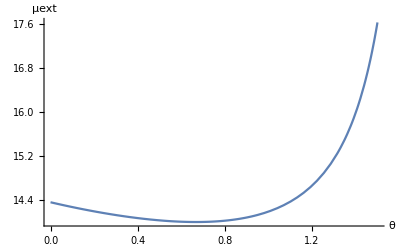

z>2 case

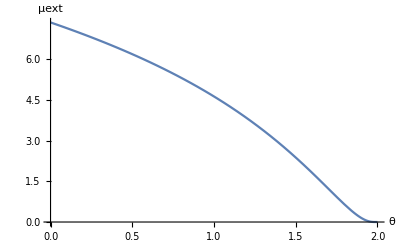

```mathematica
μextreme[uh_,z_,θ_]:=Sqrt[2(2-θ)(2+z-θ)]/uh/(z-θ)Exp[-Sqrt[(z-1+θ/2)/2/(2-θ)]];
Print["1<=z<2 case"];
Print[Plot[μextreme[0.1,1.75,θ],{θ,0,1.5},AxesLabel->{θ,μext},AxesOrigin->{0,0},PlotRange->All]];
Print["z>2 case"];
Print[Plot[μextreme[0.1,3,θ],{θ,0,2},AxesLabel->{θ,μext},AxesOrigin->{0,0},PlotRange->All]];
```

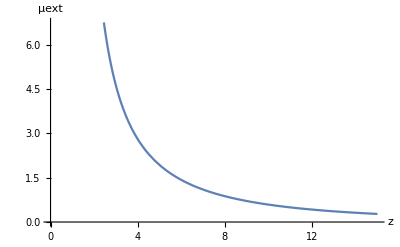

```mathematica
Print[Plot[μextreme[0.1,z,1],{z,1.5,15},AxesLabel->{z,μext},AxesOrigin->{0,0}]];
```